2021/11/21 Y . Mizoguchi
Put your libraries ‘WangTileLib.wl’ and ‘WangTilesData.wl’ on the directory ‘Desktop/20211120Yang’.
Or you should set the appropriate directory for getting libraries.

```mathematica
SetDirectory[FileNameJoin[{$HomeDirectory,"CS4/20211223/"}]];
<<Aperiodic_Wang_tile.wl;
```

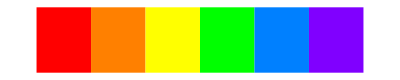

```mathematica
(*色の生成*)
Graphics[Table[{Color[i,5],Polygon[{{i,0},{i+1,0},{i+1,1},{i,1}}]},{i,0,5}]]
```

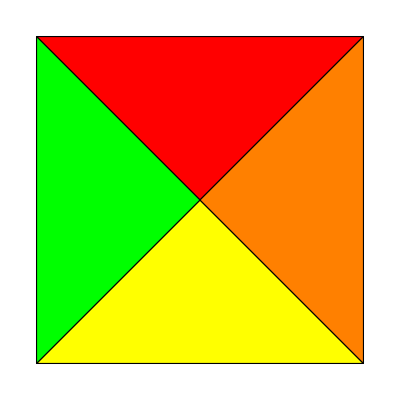
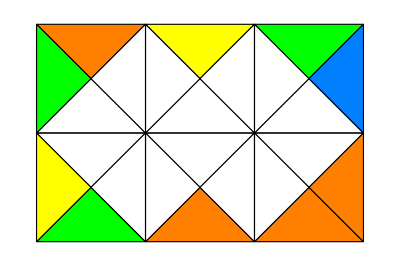

```mathematica
(*タイリングの例*)
Map[Tiling,{{{3},{1},{2},{0}},{{3,2},{4,1},{3,1,1},{1,2,3}}}]
```

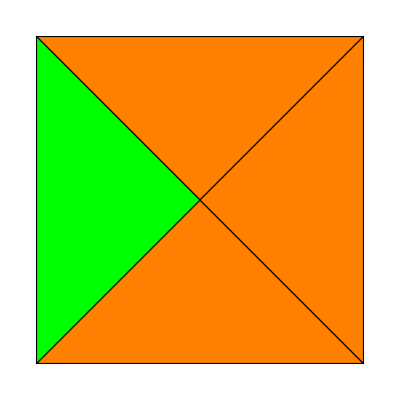
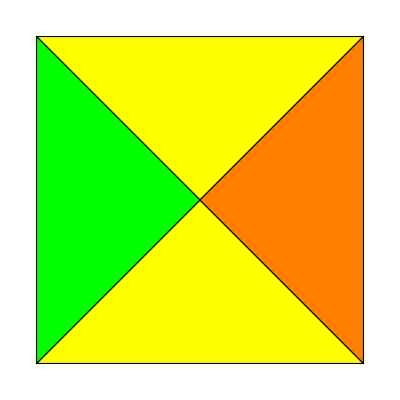
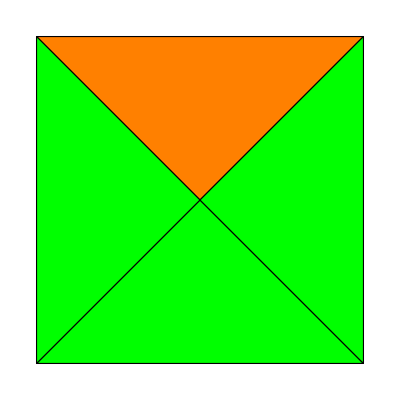
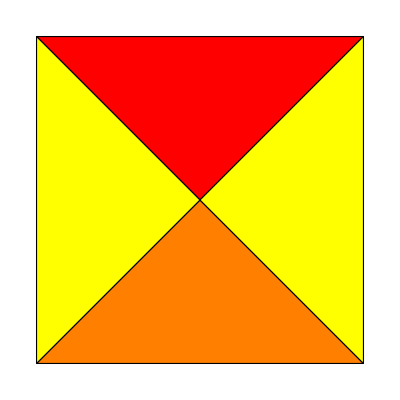
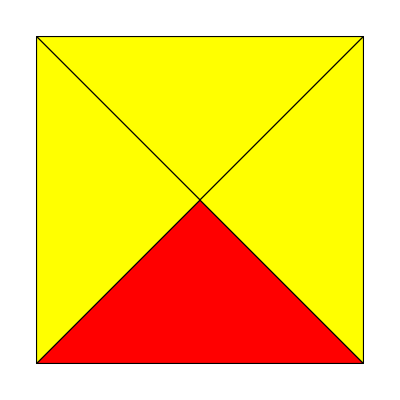
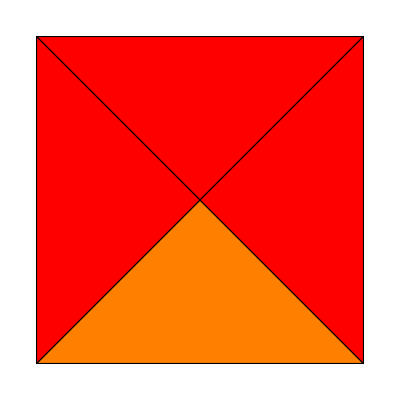
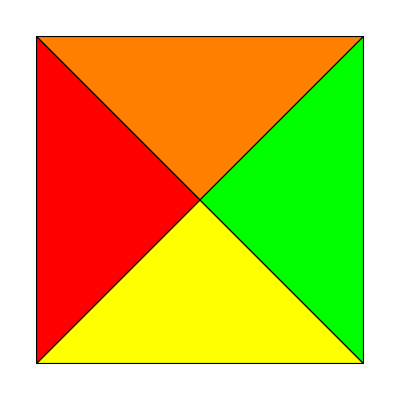
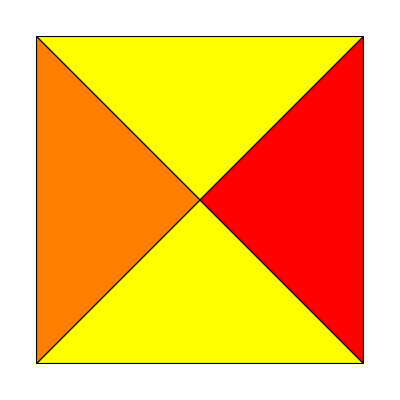

```mathematica
(*11個の非周期的なWangタイル集合*)
Map[Tiling,Jeandeltiles]
```

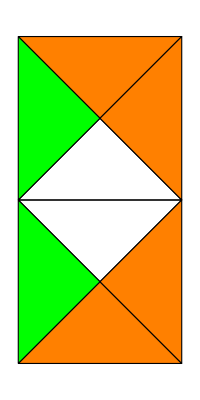
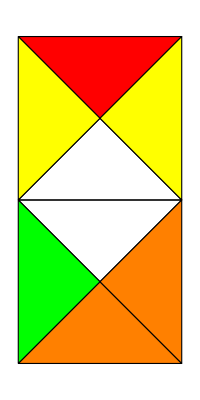
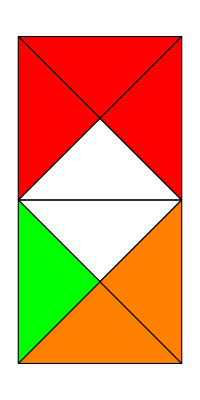
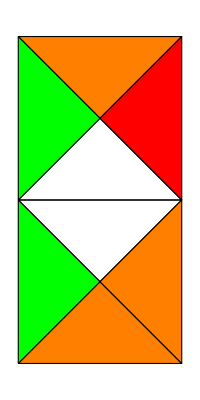
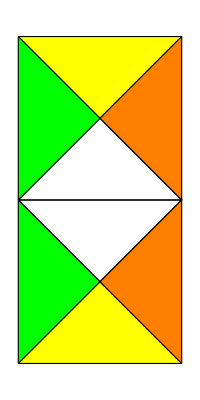
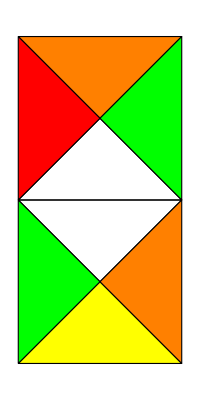
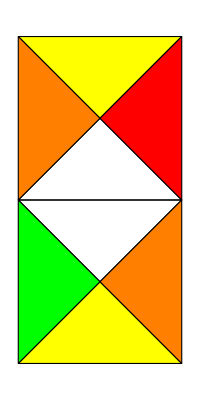
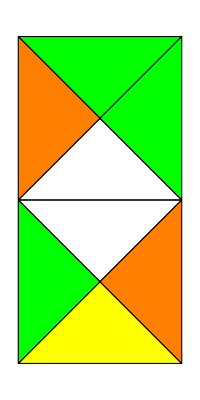

```mathematica
(*Wang集合の垂直の合成*)
Map[Tiling,Tilecompositionv[Jeandeltiles,Jeandeltiles]]
```

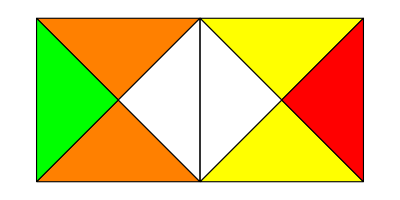
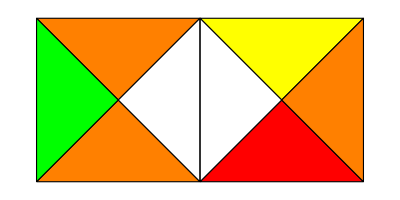
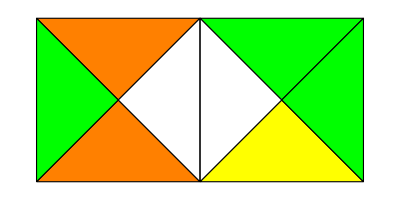
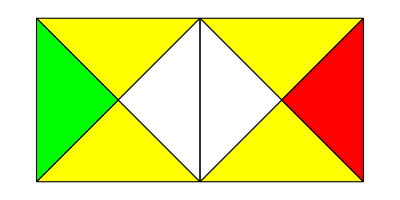
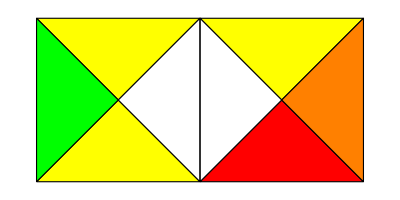
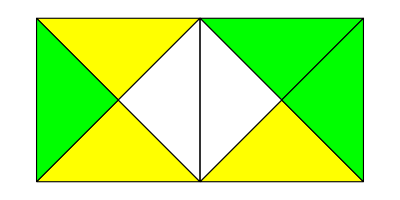
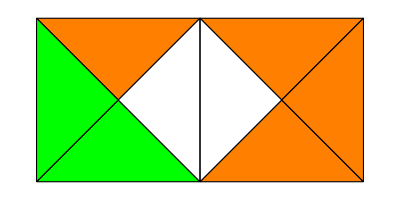
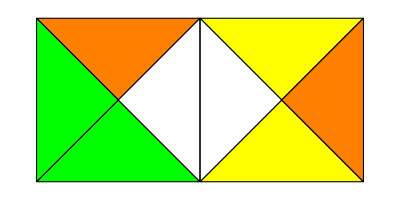

```mathematica
(*Wang集合の水平方向の合成*)
Map[Tiling,Tilecompositionh[Jeandeltiles,Jeandeltiles]]
```

```mathematica
(*エッジの数(タイルの数)=5のグラフの生成*)
qqq=Generategraphs[5]
```

{{{1,2},{2,1},{2,1},{2,1},{2,1}},{{1,2},{2,1},{2,1},{2,1},{2,2}},{{1,2},{2,1},{2,1},{2,2},{2,2}},{{1,2},{2,1},{2,2},{2,2},{2,2}},{{1,1},{1,1},{2,2},{2,2},{2,2}},{{1,1},{1,2},{2,1},{2,1},{2,2}},{{1,1},{1,2},{2,1},{2,2},{2,2}},{{1,2},{1,2},{2,1},{2,1},{2,1}},{{1,2},{1,2},{2,1},{2,1},{2,2}},{{1,2},{2,3},{3,1},{3,1},{3,1}},{{1,2},{2,3},{3,1},{3,1},{3,2}},{{1,2},{2,3},{3,1},{3,1},{3,3}},{{1,2},{2,3},{3,1},{3,2},{3,2}},{{1,2},{2,3},{3,1},{3,2},{3,3}},{{1,2},{2,3},{3,1},{3,3},{3,3}},{{1,3},{2,3},{3,1},{3,1},{3,2}},{{1,3},{2,3},{3,1},{3,2},{3,3}},{{1,2},{2,1},{2,1},{3,3},{3,3}},{{1,2},{2,1},{2,2},{3,3},{3,3}},{{1,2},{2,1},{2,3},{3,1},{3,2}},{{1,2},{2,1},{2,3},{3,1},{3,3}},{{1,2},{2,1},{2,3},{3,2},{3,3}},{{1,2},{2,2},{2,3},{3,1},{3,1}},{{1,2},{2,2},{2,3},{3,1},{3,3}},{{1,2},{2,3},{2,3},{3,1},{3,1}},{{1,2},{2,3},{2,3},{3,1},{3,2}}}

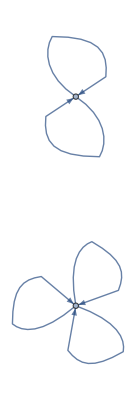
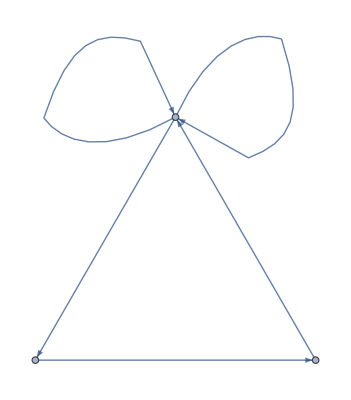
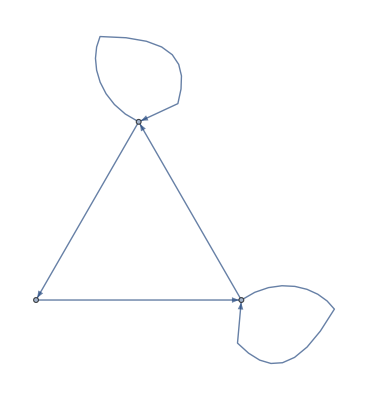
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Map[Graph,Apply[Rule,qqq,{2}]]
```

```mathematica
(*周期性の判定*)
```

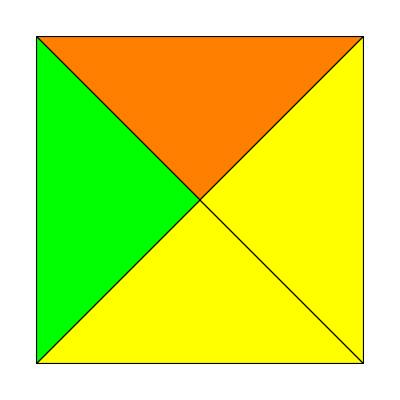
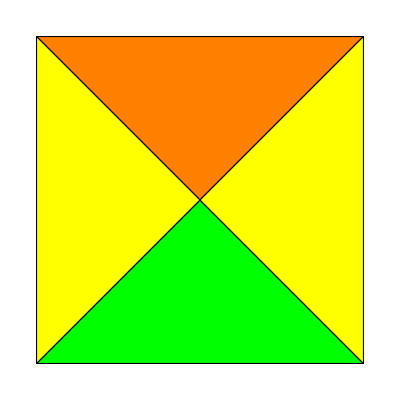
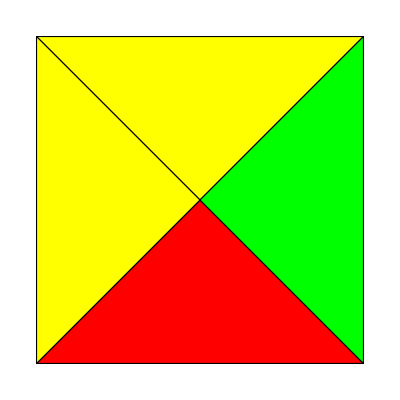
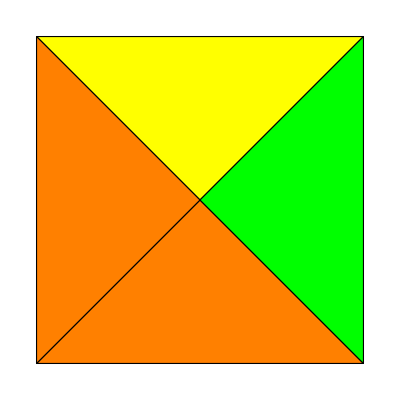
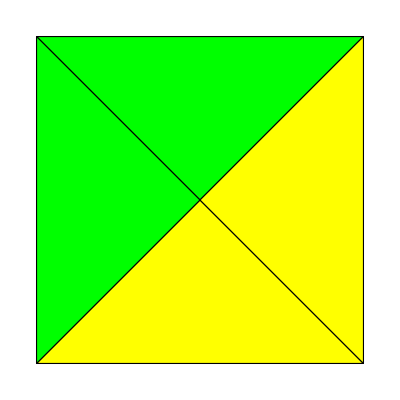
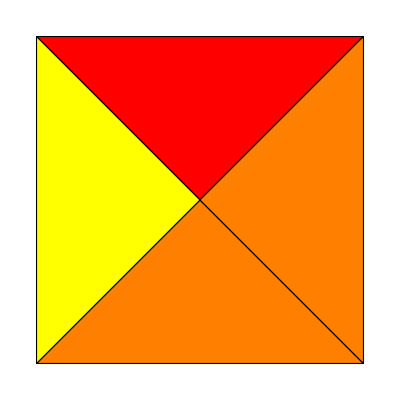
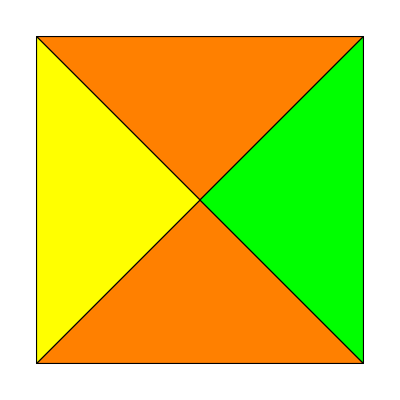
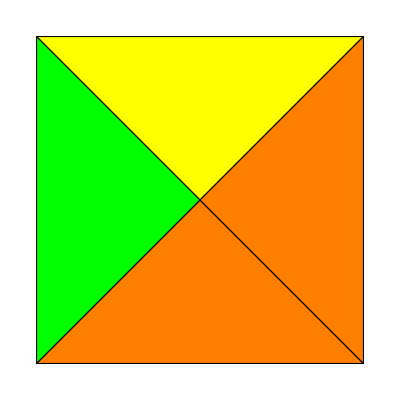

```mathematica
(*下の9個のタイルについて判定する*)
Map[Tiling,tiles1]
```

```mathematica
(*２が出力されたため、周期的であると判定*)
Nowang[tiles1][[1]]
```

2

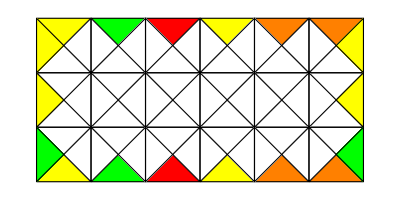

```mathematica
(*その一周期*)
Periodictile[Nowang[tiles1][[2]]]
```

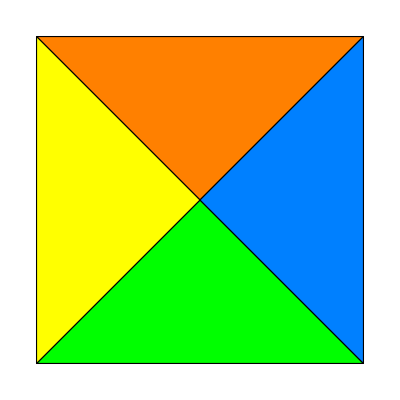
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*下の3個のタイル集合について判定*)
Map[Tiling,tiles2]
```

```mathematica
(*１が出力されたため、並べられないことがわかる*)
Nowang[tiles2][[1]]
```

1